```mathematica
n=10;
```

```mathematica
x=Table[i+RandomReal[], {i,0,10}]
```

{0.9665,1.03325,2.82883,3.80613,4.67881,5.63943,6.37539,7.1589,8.40024,9.56193,10.4139}

```mathematica
x[[1]]
```

```mathematica
t=Table[ (x[[i]]*3+2)+RandomReal[{-2,2}],{i,1,10}]
```

{5.79229,6.07394,11.9761,13.7288,15.8388,19.7597,21.1721,24.7902,27.8925,31.1715}

```mathematica
l=Table[{x[[i]],t[[i]]},{i,1,10}]
```

{{0.9665,5.79229},{1.03325,6.07394},{2.82883,11.9761},{3.80613,13.7288},{4.67881,15.8388},{5.63943,19.7597},{6.37539,21.1721},{7.1589,24.7902},{8.40024,27.8925},{9.56193,31.1715}}

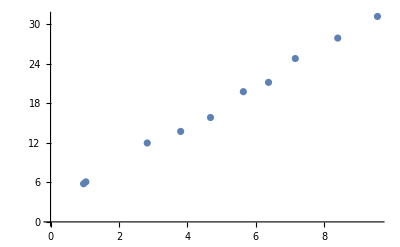

```mathematica
ListPlot[l]
```

```mathematica
σ=√Variance[t]
```

8.69708

```mathematica
term=1/(2 σ^2)(Sum[(t[[i]]-w0-w1 x[[i]])^2,{i,1,10}]+(w0^2+w1^2)/(√3))
```

0.00661034 ((31.1715-w0-9.56193 w1)^2+(27.8925-w0-8.40024 w1)^2+(24.7902-w0-7.1589 w1)^2+(21.1721-w0-6.37539 w1)^2+(19.7597-w0-5.63943 w1)^2+(15.8388-w0-4.67881 w1)^2+(13.7288-w0-3.80613 w1)^2+(11.9761-w0-2.82883 w1)^2+(6.07394-w0-1.03325 w1)^2+(5.79229-w0-0.9665 w1)^2+(w0^2+w1^2)/(√3))

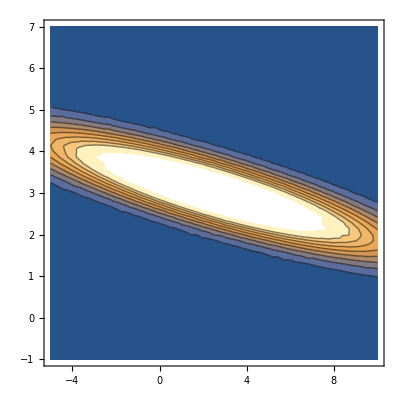

```mathematica
ContourPlot[(1/(2π σ))^(n/2+1)Exp[-term],{w0,-5,10},{w1,-1,7}]
```

```mathematica
|
```

```mathematica
Solve[{D[term,w0]==0,D[term,w1]==0},{w0,w1}]
```

{{w0→2.41635,w1→3.02555}}

```mathematica
G0=(1/(2π σ))^(n/2+1)Exp[-term]/.{{w0->2.4163483310819602,w1->3.0255538996240467}}
```

{3.47768×10^-11}

```mathematica
P=(1/(2π σ))^(n/2+1)Exp[-term]
```

3.75562×10^-11 ⅇ^(-0.00661034 ((31.1715-w0-9.56193 w1)^2+(27.8925-w0-8.40024 w1)^2+(24.7902-w0-7.1589 w1)^2+(21.1721-w0-6.37539 w1)^2+(19.7597-w0-5.63943 w1)^2+(15.8388-w0-4.67881 w1)^2+(13.7288-w0-3.80613 w1)^2+(11.9761-w0-2.82883 w1)^2+(6.07394-w0-1.03325 w1)^2+(5.79229-w0-0.9665 w1)^2+(w0^2+w1^2)/(√3)))

```mathematica
D[D[-term,w0],w0]
```

-0.13984

```mathematica
D[D[-term,w0],w1]
```

-0.666975

```mathematica
D[D[-term,w1],w0]
```

-0.666975

```mathematica
D[D[-term,w1],w1]
```

-4.39789

```mathematica
A=({{D[D[-term,w0],w0], D[D[-term,w0],w1]}, {D[D[-term,w1],w0], D[D[-term,w1],w1]}})
```

{{-0.13984,-0.666975},{-0.666975,-4.39789}}

```mathematica
({{w0, w1}}).A.({{w0}, {w1}})
```

{{w0 (-0.13984 w0-0.666975 w1)+(-0.666975 w0-4.39789 w1) w1}}

```mathematica
G=G0 Exp[w0 (-0.13983966858796143 w0-0.6669751415960573 w1)+(-0.6669751415960573 w0-4.397889104851911 w1) w1]
```

{3.47768×10^-11 ⅇ^(w0 (-0.13984 w0-0.666975 w1)+(-0.666975 w0-4.39789 w1) w1)}

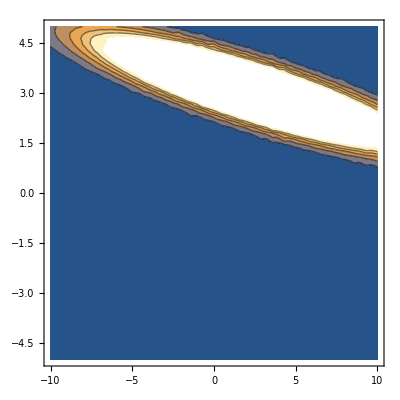

```mathematica
ContourPlot[(1/(2π σ))^(n/2+1)Exp[-term],{w0,-10,10},{w1,-5,5}]
```

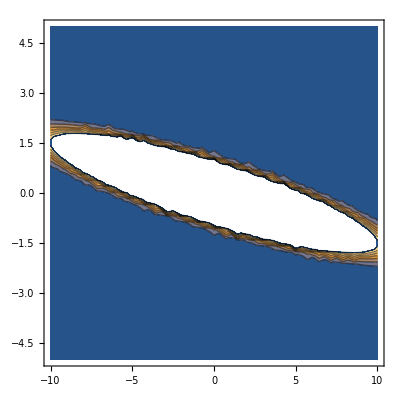

```mathematica
ContourPlot[G,{w0,-10,10},{w1,-5,5}]
```